# Plane-strain tensile Dugdale cohesive crack

```mathematica
PacletDirectoryLoad[NotebookDirectory[]<>"../../../../"]
<<BigWhamLink`
$BigWhamVersion
GetFilesDate[]
```

{/Users/bricelecampion/Documents/Work/Geomechanics/Codes/Pear/BigWhamLink/}

BigWhamLink`LTemplate`Classes`

1.2.1

{/Users/bricelecampion/Documents/Work/Geomechanics/Codes/Pear/BigWhamLink/BigWhamLink/Kernel/../LibraryResources/MacOSX-x86-64/HmatExpressions.dylib→Thu 18 Feb 2021 22:18:06GMT+1,/Users/bricelecampion/Documents/Work/Geomechanics/Codes/BigWham/cmake-build-release/libBigWham.a→Fri 12 Mar 2021 22:21:23GMT+1}

## Dugdale solution

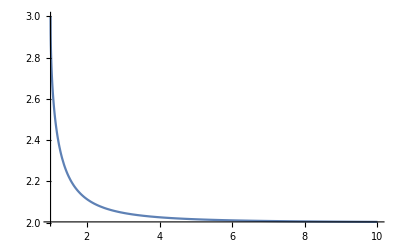

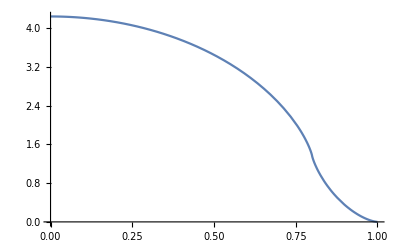

```mathematica
σy[x_]=p+2 σT/π ArcTan[Sin[π p/σT]/(Exp[2 ArcCosh[x/c]]-Cos[π p/σT])];(*stress field From the paper G.T. Hahn & A.R. Rosenfield 1964*)
wy[x_]=(4 σT)/(π Ep)1/2 (√(x^2) (Log[(-1+(√(x^2))/a √((c^2-a^2)/(c^2-x^2)))^2]-2 Log[1+(√(x^2))/a √((c^2-a^2)/(c^2-x^2))])+a (-Log[(-1+√((c^2-x^2)/(-a^2+c^2)))^2]+Log[(1+√((c^2-x^2)/(-a^2+c^2)))^2]));

Plot[σy[x]/.{σT-> 3, p-> 2,c-> 1,a-> 0.8},{x,1,10},PlotRange->All]

Plot[wy[x]/.{σT-> 3, p->2,c-> 1,a-> 0.8,Ep-> 1},{x,0,1},PlotRange->All]
```

## Mesh

```mathematica
UniformMesh[Ne_]:=Module[{h,coor,conn},
h=2/Ne;
coor=Table[{-1.+h i,0.},{i,0,Ne}];
conn=Table[{i,i+1},{i,1,Ne}];
<|"Coordinates"-> coor,"Connectivity"-> conn,"Nelts"-> Ne|> 
]
```

```mathematica
GeometricMesh[Ne_,β_]:=Module[{xx,geoprog,coor,conn},
geoprog=Table[ i^β,{i,1,Floor[Ne/2]}];
xx={-Reverse[Accumulate[1.Reverse[geoprog]/Total[geoprog]]] ,0.,Accumulate[Reverse[1.geoprog/Total[geoprog]]]}//Flatten;
coor={#,0.}& /@ xx;
conn=Table[{i,i+1},{i,1,Length[coor]-1}];
<|"Coordinates"-> coor,"Connectivity"-> conn,"Nelts"-> Length[conn]|> 
]
```

## S3DP0 uniform mesh

```mathematica
Rock=<|"Young"-> 1,"Poisson"-> 0.|>;
Ep=Rock["Young"]/(1-Rock["Poisson"]^2);
```

```mathematica
Params={c-> 1.,p-> 1.,σT-> 2.}
```

{c→1.,p→1.,σT→2.}

```mathematica
Xcoh=c/Sec[(π p)/(2 σT) ] /.Params
```

0.707107

```mathematica
Params=Join[Params,{a-> Xcoh}]
```

{c→1.,p→1.,σT→2.,a→0.707107}

```mathematica
Nel=40;
```

```mathematica
mesh=UniformMesh[Nel];
```

```mathematica
ker="S3DP0"; 
ml=100; (* max leaf size - 100 is a good start *)
eta=3;  (* eta  - 3 is a good start (0 for no compression) *)
eps=0.001;  (* no 0.001 *)
prop={Rock["Young"],Rock["Poisson"],10000.}; (* E, ν *) 
h1=toHMatExpr[mesh["Coordinates"],mesh["Connectivity"],ker,prop,ml,eta,eps]
```

constructor called

Now setting up and constructing the HMatrix ...

HMatrix is now set !

BigWhamLink`LTemplate`Classes`HMatExpr[8]

```mathematica
xmid=Mean[mesh["Coordinates"][[#]]][[1]] &/@ mesh["Connectivity"];
```

```mathematica
Load=ConstantArray[0.,2 Nel];
Load[[2;;-1;;2]]=p/.Params;
```

```mathematica
jcoh=Position[xmid,_?(Abs[#]>Xcoh&)]//Flatten;
Load[[jcoh 2] ]= (p-σT)/.Params;
```

```mathematica
(* Solution via iterative Solve *)
fdot[x_?(VectorQ[#,NumericQ]&)]:=Hdot[h1,x];
{sol,stats}=Reap@LinearSolve[fdot,Load,Method->{"Krylov",{"Method"->"BiCGSTAB"(*"GMRES"*)(*"BiCGSTAB"*),(*"Preconditioner"->precJ,"PreconditionerSide"->Right,*)(*"StartingVector"->v0,*)"Tolerance"->10^-6.,"MaxIterations"->1000,"ResidualNormFunction"->((Sow[Norm[#,2]])&)}}];
ds=sol[[1;;-1;;2]];dn=sol[[2;;-1;;2]];
```

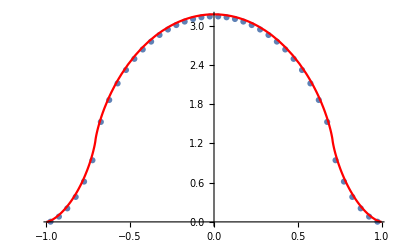

```mathematica
Show[ListPlot[Transpose[{xmid,dn}],PlotMarkers->Automatic],Plot[wy[Abs[x]]/.Params,{x,-1,1},PlotStyle->Red]]
```

```mathematica
relerr=Abs[1-dn/(wy[Abs[xmid]]/.Params)];
abserr=Abs[ dn-(wy[Abs[xmid]]/.Params)];
```

```mathematica
abserr //Max
```

0.092617

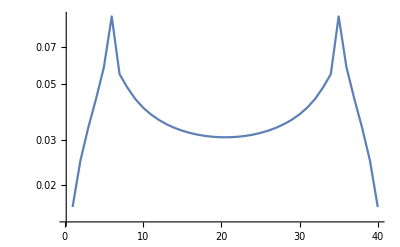

```mathematica
ListLogPlot[ abserr,PlotRange->All,Joined->True]
```

## S3DP0 Geo mesh

```mathematica
Rock=<|"Young"-> 1,"Poisson"-> 0.|>;
Ep=Rock["Young"]/(1-Rock["Poisson"]^2);
```

```mathematica
Params={c-> 1.,p-> 1.,σT-> 2.}
```

{c→1.,p→1.,σT→2.}

```mathematica
Xcoh=c/Sec[(π p)/(2 σT) ] /.Params
```

0.707107

```mathematica
Params=Join[Params,{a-> Xcoh}]
```

{c→1.,p→1.,σT→2.,a→0.707107}

```mathematica
Nel=40;
```

```mathematica
mesh=.;
```

```mathematica
mesh=GeometricMesh[Nel,1.3];
```

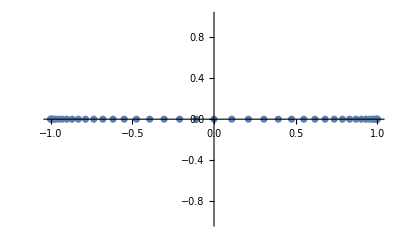

```mathematica
ListPlot[mesh["Coordinates"]]
```

```mathematica
xmid=Mean[mesh["Coordinates"][[#]]][[1]] &/@ mesh["Connectivity"];
```

```mathematica
ker="S3DP0"; 
ml=100; (* max leaf size - 100 is a good start *)
eta=3;  (* eta  - 3 is a good start (0 for no compression) *)
eps=0.001;  (* no 0.001 *)
prop={Rock["Young"],Rock["Poisson"],10000.}; (* E, ν *) 
h1=toHMatExpr[mesh["Coordinates"],mesh["Connectivity"],ker,prop,ml,eta,eps]
```

constructor called

Now setting up and constructing the HMatrix ...

HMatrix is now set !

BigWhamLink`LTemplate`Classes`HMatExpr[15]

```mathematica
GetCollocationPoints[h1][[;;,1]]==xmid
```

True

```mathematica
Load=ConstantArray[0.,2 mesh["Nelts"]];
Load[[2;;-1;;2]]=p/.Params;
```

```mathematica
jcoh=Position[xmid,_?(Abs[#]>Xcoh&)]//Flatten;
Load[[jcoh 2] ]= (p-σT)/.Params;
```

```mathematica
(* Solution via iterative Solve *)
fdot[x_?(VectorQ[#,NumericQ]&)]:=Hdot[h1,x];
{sol,stats}=Reap@LinearSolve[fdot,Load,Method->{"Krylov",{"Method"->"BiCGSTAB"(*"GMRES"*)(*"BiCGSTAB"*),(*"Preconditioner"->precJ,"PreconditionerSide"->Right,*)(*"StartingVector"->v0,*)"Tolerance"->10^-6.,"MaxIterations"->1000,"ResidualNormFunction"->((Sow[Norm[#,2]])&)}}];
ds=sol[[1;;-1;;2]];dn=sol[[2;;-1;;2]];
```

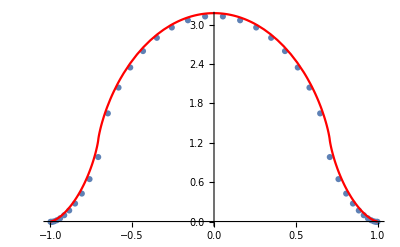

```mathematica
Show[ListPlot[Transpose[{xmid,dn}],PlotMarkers->Automatic],Plot[wy[Abs[x]]/.Params,{x,-1,1},PlotStyle->Red]]
```

```mathematica
relerr=Abs[1-dn/(wy[Abs[xmid]]/.Params)];
abserr=Abs[ dn-(wy[Abs[xmid]]/.Params)];
```

```mathematica
abserr //Max
```

0.254278

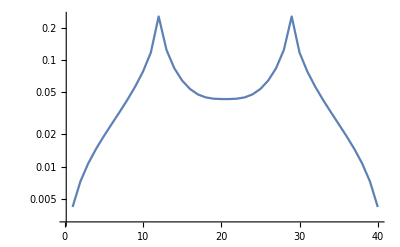

```mathematica
ListLogPlot[ abserr,PlotRange->All,Joined->True]
```

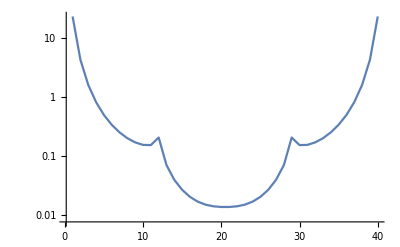

```mathematica
ListLogPlot[ relerr,PlotRange->All,Joined->True]
```

## 2DP1 Geo mesh

```mathematica
Rock=<|"Young"-> 1,"Poisson"-> 0.|>;
Ep=Rock["Young"]/(1-Rock["Poisson"]^2);
```

```mathematica
Params={c-> 1.,p-> 1.,σT-> 2.}
```

{c→1.,p→1.,σT→2.}

```mathematica
Xcoh=c/Sec[(π p)/(2 σT) ] /.Params
```

0.707107

```mathematica
Params=Join[Params,{a-> Xcoh}]
```

{c→1.,p→1.,σT→2.,a→0.707107}

```mathematica
Nel=40;
```

```mathematica
mesh=.;
```

```mathematica
mesh=GeometricMesh[Nel,2.];
```

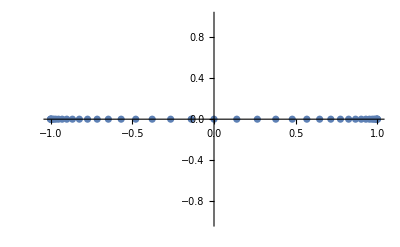

```mathematica
ListPlot[mesh["Coordinates"]]
```

```mathematica
xmid=Mean[mesh["Coordinates"][[#]]][[1]] &/@ mesh["Connectivity"];
```

```mathematica
ker="2DP1"; 
ml=100; (* max leaf size - 100 is a good start *)
eta=3;  (* eta  - 3 is a good start (0 for no compression) *)
eps=0.001;  (* no 0.001 *)
prop={Rock["Young"],Rock["Poisson"]}; (* E, ν *) 
h1=toHMatExpr[mesh["Coordinates"],mesh["Connectivity"],ker,prop,ml,eta,eps]
```

constructor called

Now setting up and constructing the HMatrix ...

HMatrix is now set !

BigWhamLink`LTemplate`Classes`HMatExpr[3]

```mathematica
Xcol=GetCollocationPoints[h1][[;;,1]]
```

{-0.999949,-0.999703,-0.999447,-0.998462,-0.997799,-0.995581,-0.994306,-0.990363,-0.988271,-0.982112,-0.978999,-0.97013,-0.965792,-0.95372,-0.947954,-0.932186,-0.924787,-0.90483,-0.895594,-0.870956,-0.859679,-0.829868,-0.816346,-0.780867,-0.764896,-0.723258,-0.704633,-0.656343,-0.63486,-0.579425,-0.554881,-0.491808,-0.463999,-0.392795,-0.361516,-0.281689,-0.246736,-0.157793,-0.118962,-0.0204107,0.0204107,0.118962,0.157793,0.246736,0.281689,0.361516,0.392795,0.463999,0.491808,0.554881,0.579425,0.63486,0.656343,0.704633,0.723258,0.764896,0.780867,0.816346,0.829868,0.859679,0.870956,0.895594,0.90483,0.924787,0.932186,0.947954,0.95372,0.965792,0.97013,0.978999,0.982112,0.988271,0.990363,0.994306,0.995581,0.997799,0.998462,0.999447,0.999703,0.999949}

```mathematica
Load=ConstantArray[0.,4 mesh["Nelts"]];
Load[[2;;-1;;2]]=p/.Params;
```

```mathematica
jcoh=Position[Xcol,_?(Abs[#]>Xcoh&)]//Flatten;
Load[[jcoh 2] ]= (p-σT)/.Params;
```

```mathematica
(* Solution via iterative Solve *)
fdot[x_?(VectorQ[#,NumericQ]&)]:=Hdot[h1,x];
{sol,stats}=Reap@LinearSolve[fdot,Load,Method->{"Krylov",{"Method"->"BiCGSTAB"(*"GMRES"*)(*"BiCGSTAB"*),(*"Preconditioner"->precJ,"PreconditionerSide"->Right,*)(*"StartingVector"->v0,*)"Tolerance"->10^-6.,"MaxIterations"->1000,"ResidualNormFunction"->((Sow[Norm[#,2]])&)}}];
ds=sol[[1;;-1;;2]];dn=sol[[2;;-1;;2]];
```

```mathematica
xb=(mesh["Coordinates"][[#,1]] & /@ mesh["Connectivity"])//Flatten
```

{-1.,-0.999652,-0.999652,-0.998258,-0.998258,-0.995122,-0.995122,-0.989547,-0.989547,-0.980836,-0.980836,-0.968293,-0.968293,-0.95122,-0.95122,-0.92892,-0.92892,-0.900697,-0.900697,-0.865854,-0.865854,-0.823693,-0.823693,-0.773519,-0.773519,-0.714634,-0.714634,-0.646341,-0.646341,-0.567944,-0.567944,-0.478746,-0.478746,-0.378049,-0.378049,-0.265157,-0.265157,-0.139373,-0.139373,0.,0.,0.139373,0.139373,0.265157,0.265157,0.378049,0.378049,0.478746,0.478746,0.567944,0.567944,0.646341,0.646341,0.714634,0.714634,0.773519,0.773519,0.823693,0.823693,0.865854,0.865854,0.900697,0.900697,0.92892,0.92892,0.95122,0.95122,0.968293,0.968293,0.980836,0.980836,0.989547,0.989547,0.995122,0.995122,0.998258,0.998258,0.999652,0.999652,1.}

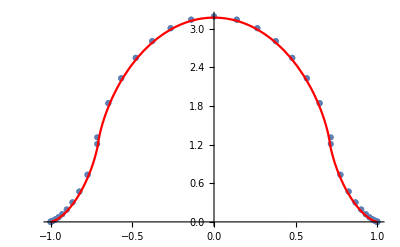

```mathematica
Show[ListPlot[Transpose[{xb,dn}],PlotMarkers->Automatic],Plot[wy[Abs[x]]/.Params,{x,-1,1},PlotStyle->Red]]
```

```mathematica
relerr=Abs[1-dn/(wy[Abs[xb]]/.Params)];
abserr=Abs[ dn-(wy[Abs[xb]]/.Params)];
```

```mathematica
abserr //Max
```

0.172611

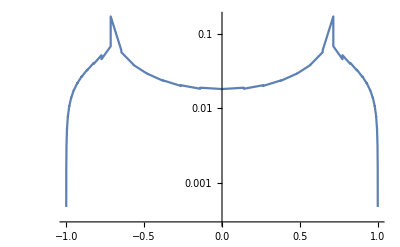

```mathematica
ListLogPlot[{xb, abserr}//Transpose,PlotRange->All,Joined->True]
```

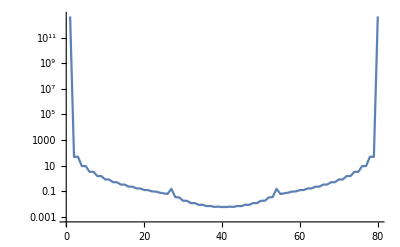

```mathematica
ListLogPlot[ relerr,PlotRange->All,Joined->True]
```